# Q3 Application

Q3 is a software package written in the Wolfram Language  to help study quantum information systems, quantum many-body systems, and quantum spin systems. It provides various tools and utilities for symbolic and numerical calculations in these areas of quantum physics.

## Installation

Q3 is distributed through the GitHub repository, https://github.com/quantum-mob/Q3App. It provides a fully automatic installation and update. Just evaluate (press the key combination Shift-Enter) the following code:

```mathematica
Module[{ps},ps=PacletSiteRegister["https://github.com/quantum-mob/PacletServer/raw/main","Quantum Mob Paclet Server"];
PacletSiteUpdate[ps];
PacletInstall["Q3"]
]
```

Once Q3 is installed, use Q3CheckUpdate and Q3Update to check for updates and install an update remotely.

## Quick Start

Once Q3 is installed, put Q3 or Q3/guide/Q3 in the search field of the Wolfram Language Documentation Center (Mathematica help window) to get detailed technical information about the application . It will give you users' guides and tutorials .

## A Quick Look

Make sure that the Q3 package is loaded.

```mathematica
<<Q3`
```

### Quantum Information Systems

```mathematica
Let[Qubit,S]
```

```mathematica
out=S[1,6]**S[2,6]**S[3,6]**Ket[]
```

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

```mathematica
Matrix[out]//Normal
```

{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}

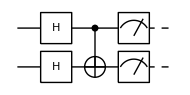

```mathematica
qc=QuantumCircuit[S[{1,2},6],CNOT[S[1],S[2]],Measurement[S[{1,2},3]]]
```

### Quantum Many-Body Systems

```mathematica
Let[Fermion,c]
```

```mathematica
bs=Basis[c@{1,2}]
```

{0_c_10_c_2,0_c_11_c_2,1_c_10_c_2,1_c_11_c_2}

```mathematica
H=Q@c@{1,2}
```

c_1^†c_1+c_2^†c_2

```mathematica
H**bs
```

{0,0_c_11_c_2,1_c_10_c_2,2 1_c_11_c_2}

### Quantum Spin Systems

```mathematica
Let[Spin,J]
```

```mathematica
H=J[1,1]**J[2,1]+J[1,2]**J[2,2]
```

J_1^XJ_2^X+J_1^YJ_2^Y

```mathematica
v=Ket[J[1]->-1/2]+Ket[J[2]->-1/2]//KetRegulate
```

(-1/2)_J_1(1/2)_J_2+(1/2)_J_1(-1/2)_J_2

```mathematica
vv=H**v
```

1/2 (-1/2)_J_1(1/2)_J_2+1/2 (1/2)_J_1(-1/2)_J_2